#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
(*Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]*)
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
ClearAll;
ImgSize=900;
SetDirectory["/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];
parity="-";
jJ=1;
mJs=Range[-jJ,jJ,1];
thresholdLIT=10^(-13);
thresholdD=thresholdLIT;
mom=ReadList["INEN",Number,RecordLists->True][[7]][[1]]
```

10.

```mathematica
Clear[matSqrts];matSqrts[norm_,cutoff_:0]:=Block[{es=Eigensystem[norm],ovsqi,ovsq,n},Print["min/max: ",MinMax[Re[es[[1]]]]];n=Length[Select[Re[es[[1]]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[Re[es[[1]]],#<cutoff&]]];n=Length[Select[Re[es[[1]]],#<cutoff&]];ovsq=DiagonalMatrix[SparseArray[If[#<cutoff,0,Sqrt[#]]&/@Re[es[[1]]]]];ovsqi=DiagonalMatrix[SparseArray[If[#<cutoff,0,1/Sqrt[#]]&/@Re[es[[1]]]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]
```

### Read LHS ⟨ ϕ_D^n|(Ĥ)_(V18+UIX)|ϕ_D^m ⟩, m,n∈{1,N_D}

```mathematica
DNormHamMat=readREAL8list["./deuteron/MATOUTB"];
DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}];
```

```mathematica
{DNmh,DNmhi}=matSqrts[DNorm,0];
```

min/max: {6.41486×10^-7,7.67977}

(min/max) discarded elements: 0 {∞,-∞}

```mathematica
tst=Transpose[DNmhi].DNorm.DNmhi;
```

#### Check zero mode norm eigenvectors are approximately zero mode eigenvectors of H

```mathematica
tv=Transpose[Eigensystem[DNorm]][[-2]];
```

```mathematica
tv[[1]]
```

0.0000119041

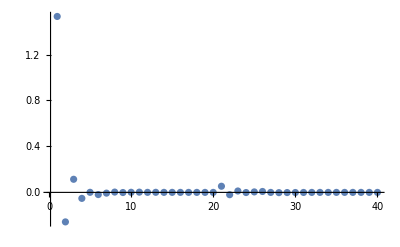

```mathematica
ListPlot[Chop[DHam.tv[[2]],10^-6],PlotRange->Full]
```

```mathematica
tv=Transpose[Eigensystem[DNorm]][[-4]];
```

```mathematica
tv[[1]]
```

0.0000609181

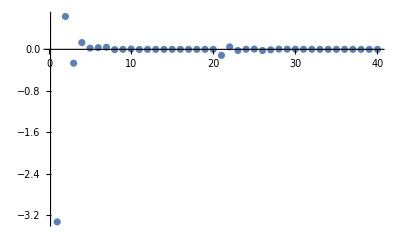

```mathematica
ListPlot[Chop[DHam.tv[[2]],10^-7],PlotRange->Full]
```

#### The real calculation

Set a sensible cut-off

min/max: {6.41486×10^-7,7.67977}

(min/max) discarded elements: 0 {∞,-∞}

B(D) = -2.24016

Dim_full^deuteron = 40=^!40   ;     Dim_(non - singular)^deuteron = 40

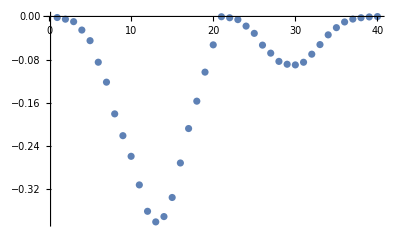

```mathematica
randomBasisIndices=Range[1,DBasisDim,1];
redDham=DHam[[randomBasisIndices,randomBasisIndices]];
redDnorm=DNorm[[randomBasisIndices,randomBasisIndices]];

{DNmh,DNmhi}=matSqrts[redDnorm,thresholdD];

{e0,v0}=Sort[Transpose[Eigensystem[tst=Transpose[DNmhi].redDham.DNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["B(D) = ",e0];
Print["Dim_full^deuteron = ",Dimensions[DNorm][[1]],"=^!",DBasisDim,"   ;     Dim_(non - singular)^deuteron = ",Dimensions[v0][[1]]]
fullv0=Normalize[Transpose[DNmh].v0];
ListPlot[Re[fullv0],PlotRange->Full]
```

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
LitNormHamMat=readREAL8list["./lhs/MATOUTB"];
LITbasisDim=IntegerPart[Sqrt[Length[LitNormHamMat] 0.5]];
LitNorm=ArrayReshape[LitNormHamMat[[1;;LITbasisDim^2]],{LITbasisDim,LITbasisDim}];LitHam=ArrayReshape[LitNormHamMat[[LITbasisDim^2+1;;]],{LITbasisDim,LITbasisDim}];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = 20

min/max: {4.6921×10^-6,6.06747}

(min/max) discarded elements: 0 {∞,-∞}

0.0878431

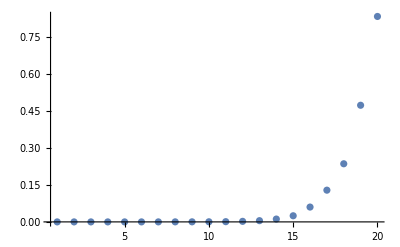

```mathematica
{LitNmh,LitNmhi}=matSqrts[LitNorm,thresholdLIT];
{e0l,v0l}=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam.LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
e0l
fullv0l=Normalize[Transpose[LitNmh].v0l];
ListPlot[Re[fullv0l],PlotRange->Full]
```

#### Check zero mode norm eigenvectors are approximately zero mode eigenvectors of H

```mathematica
tv=Transpose[Eigensystem[LitNorm]][[-2]];
```

```mathematica
tv[[1]]
```

0.0000765734

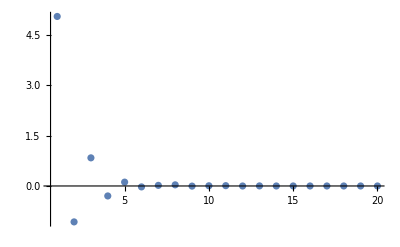

```mathematica
ListPlot[Chop[LitHam.tv[[2]],10^-16],PlotRange->Full]
```

```mathematica
tv=Transpose[Eigensystem[LitNorm]][[-4]];
```

```mathematica
tv[[1]]
```

0.000770177

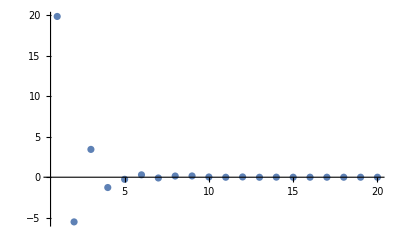

```mathematica
ListPlot[Chop[LitHam.tv[[2]],10^-17],PlotRange->Full]
```

#### Read RHS ⟨ ϕ_(lit+He3)^n|O_Lm_L|ϕ_(lit+He3)^m ⟩, n,m∈{1,N_LIT/n_k+N_He3}

the calculation is parallel in n_k parts

```mathematica
nk=Max[ToExpression[StringSplit[FileNames["*_inhomo*"],"_"][[All,1]]]];
ks=Range[0,nk];
files="./0_inhomo_"<>ToString[#]&/@ks;

inhomos=SparseArray[readREAL8list[#]]&/@files;
CouplingMatrices=SparseArray[ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]]&/@inhomos;
CouplingBloxx=#[[DBasisDim+1;;,;;DBasisDim]]&/@CouplingMatrices;
dims=Dimensions[#]&/@CouplingBloxx;
CouplingBlock=ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],DBasisDim}];

Print["Dim(⟨ψ|ο̂|deuteron⟩) = ",Dimensions[CouplingBlock]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

Dim(⟨ψ|ο̂|deuteron⟩) = {20,40}

Dim(⟨ψ|Ĥ|ψ⟩) = {20,20}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {20,20}

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=5.;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
testfu=0;
```

```mathematica
Clear[normreg];
normreg[threshold_,noMa_]:=Block[
{es=Eigensystem[noMa],μ,transf,μs,Or},
{μ,transf}=Transpose[Select[Sort[Transpose[es],Re[#1[[1]]]<Re[#2[[1]]]&],Re[#[[1]]]>threshold&]];
If[Dimensions[μ]<Dimensions[es[[1]]],
{μs,Or}=Transpose[Select[Sort[Transpose[es],Re[#1[[1]]]<Re[#2[[1]]]&],Re[#[[1]]]<=threshold&]];
,{μs,Or}={{},{}}];
{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}];

Clear[decompose];
decompose[thresholdHE_,thresholdLIT_,HENorm_,HEHam_,LITNorm_,LITHam_,LITYHE_]:= Block[{OμRHS,OrRHS,μsRHS,λsHe,trfHe,OμLHS,OrLHS,μsLHS,λsLit,trfLit},
{OμRHS,OrRHS,μsRHS}=normreg[thresholdHE,HENorm];
{λsHe,trfHe}=Eigensystem[(Transpose[OμRHS].HEHam).OμRHS];

e0=Min[Re[λsHe]];
Print["E_0( th=",N[thresholdHE]," ) = ",e0];


{OμLHS,OrLHS,μsLHS}=normreg[thresholdLIT,LITNorm];
{λsLit,trfLit}=Eigensystem[(Transpose[OμLHS].LITHam).OμLHS];

inhomo=(2/mom) (Transpose[OμLHS].(LITYHE.OμRHS)).trfHe[[1]];
{λsLit,trfLit.inhomo}
];
Clear[litcomp];
litcomp[thresholdHE_,thresholdLIT_,HENorm_,HEHam_,LITNorm_,LITHam_,LITYHE_]:=Block[{λscf=Transpose[decompose[thresholdHE,thresholdLIT,HENorm,HEHam,LITNorm,LITHam,LITYHE]]},
Plus@@((Abs[#[[2]]]^2/((#[[1]]-Re[e0]-σRe)^2+σI^2))&/@λscf)];
```

```mathematica
LIT={};
binbeg=1;
binend=18;
bindel=0;
MaxFragmentIDX=Total[dims[[All,1]][[;;#]]]&/@Range[1,Length[dims]];
MaxFragmentIDX=Prepend[MaxFragmentIDX,0]

randomBasisIndicesD=Range[1,Min[1182,DBasisDim],1];

dimss=1;

Do[
(*randomBasisIndices=Sort[RandomSample[Range[1,MaxFragmentIDX[[bin]]],dimen]];*)
bvstart=MaxFragmentIDX[[binbeg]]+dimen;
randomBasisIndices=Range[bvstart,MaxFragmentIDX[[Min[binend,Dimensions[MaxFragmentIDX][[1]]]]],1];

If[bindel≠0,
randomBasisIndices=Select[randomBasisIndices,#>MaxFragmentIDX[[bindel+1]]||#<=MaxFragmentIDX[[bindel]]&]];

(*randomBasisIndices=Union[randomBasisIndices,Range[1,113]]*);

redLITham=LitHam[[randomBasisIndices,randomBasisIndices]];
redLITnorm=LitNorm[[randomBasisIndices,randomBasisIndices]];
redCPLblock=CouplingBlock[[randomBasisIndices,randomBasisIndicesD]];

thresholdLIT=5^(-7);

minth=1.5^(-1) thresholdLIT;maxth=thresholdLIT;nth=10;
If[nth==1,thresholdrng={thresholdLIT},thresholdrng=Range[minth,maxth,(maxth-minth)/nth]];

testfu=Evaluate[litcomp[#,#,DNorm[[randomBasisIndicesD,randomBasisIndicesD]],DHam[[randomBasisIndicesD,randomBasisIndicesD]],redLITnorm,redLITham,redCPLblock]&/@thresholdrng];
AppendTo[LIT,{(-1)^(jJ-1) #,randomBasisIndices}]&/@testfu;
,{dimen,dimss}]

#[[;;10]]&/@LIT[[All,2]]//MatrixForm
LITs=LIT[[All,1]]/.σRe->σRs;
dimlegend=("Lit-basis dim = "<>ToString[#]&/@First[#]&/@LIT[[All,2]]);
thrlegend=("λ_𝟙="<>ToString[#,TraditionalForm]&/@thresholdrng);
plote=ListPlot[Transpose[{σRs,Flatten[#]}]&/@LITs,PlotLabel->Style["σ_I = "<>ToString[σI],18,Red],AxesLabel->{Style["σ_R [MeV]",Gray,18],Style["LIT [MeV^-4]",Red,18]},PlotLegends->Placed[thrlegend,Above],LabelStyle->12,ImageSize->ImgSize,PlotRange->Full];
Export["plot.pdf",plote,"PDF","AllowRasterization"->False]
```

{0,20}

E_0( th=8.53333×10^-6 ) = -2.24016

E_0( th=8.96×10^-6 ) = -2.24016

E_0( th=9.38667×10^-6 ) = -2.24016

E_0( th=9.81333×10^-6 ) = -2.24016

E_0( th=0.00001024 ) = -2.24016

E_0( th=0.0000106667 ) = -2.24016

E_0( th=0.0000110933 ) = -2.24016

E_0( th=0.00001152 ) = -2.24016

E_0( th=0.0000119467 ) = -2.24016

E_0( th=0.0000123733 ) = -2.24016

E_0( th=0.0000128 ) = -2.24016

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10)

plot.pdf

E_0( th=1.×10^-6 ) = -2.24016

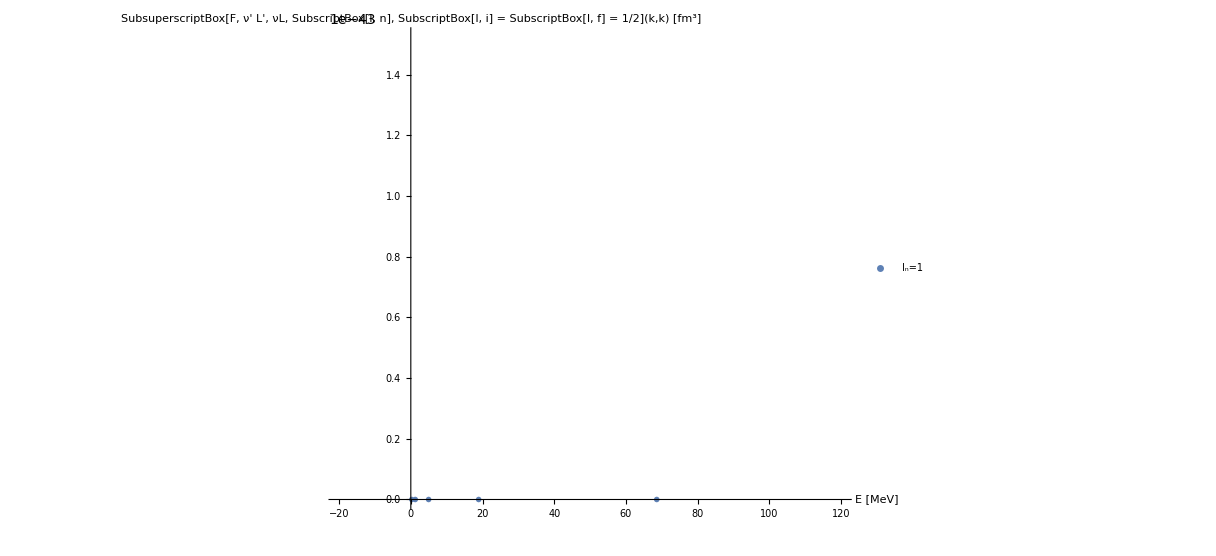

```mathematica
strengthfunctionBare={};
evupplim=10^19;
Do[
(*randomBasisIndices=Sort[RandomSample[Range[1,MaxFragmentIDX[[bin]]],dimen]];*)
randomBasisIndices=Range[MaxFragmentIDX[[binbeg]]+dimen,MaxFragmentIDX[[Min[binend,Dimensions[MaxFragmentIDX][[1]]]]],2];

redLITham=LitHam[[randomBasisIndices,randomBasisIndices]];
redLITnorm=LitNorm[[randomBasisIndices,randomBasisIndices]];
redCPLblock=CouplingBlock[[randomBasisIndices,All]];

LITcompo=Re[Transpose[decompose[thresholdLIT,thresholdLIT,DNorm,DHam,redLITnorm,redLITham,redCPLblock]]];

LITcompo=Transpose[{LITcompo[[All,1]],Re[(-1)^(jJ-0.5) LITcompo[[All,2]]]}];
AppendTo[strengthfunctionBare,Transpose[{LITcompo[[All,1]],(LITcompo[[All,2]]^2)}]];
,{dimen,dimss}]

ListPlot[Select[strengthfunctionBare[[1]],(#[[2]]<evupplim)&],Joined->False,PlotMarkers->{♪,22},Filling->Axis,FillingStyle->Green,PlotRange->{{-20,120},Full},AxesLabel->{Style["E [MeV]",Blue,18],Style["SubsuperscriptBox[F, ν' L', νL, SubscriptBox[I, n], SubscriptBox[I, i] = SubscriptBox[I, f] = 1/2](k,k) [fm^3]",Blue,18]},PlotStyle->{},PlotLegends->{"I_n="<>ToString[jJ]},ImageSize->ImgSize]
```

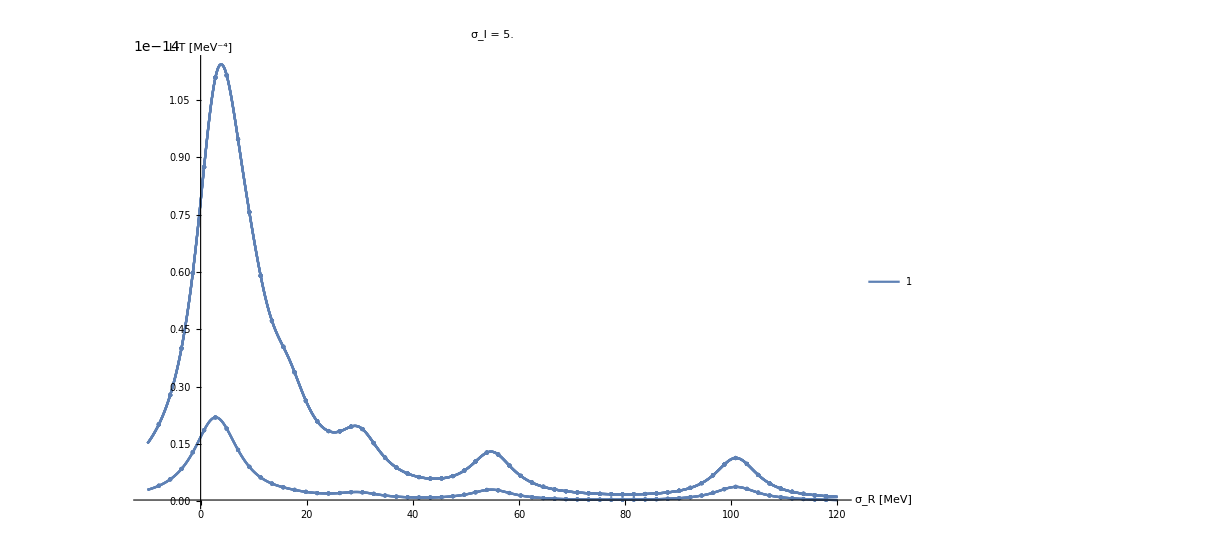

```mathematica
dimens=Length[#]&/@LIT[[All,2]];
Plot[LIT[[All,1]],{σRe,-10,120},PlotRange->{Automatic,Full},MaxRecursion->0,PlotPoints->500,MeshFunctions->{#&},Mesh->60,MeshStyle->PointSize[Large],
PlotLabel->Style["σ_I = "<>ToString[σI],18,Red],AxesLabel->{Style["σ_R [MeV]",Gray,18],Style["LIT [MeV^-4]",Red,18]},ImageSize->ImgSize,PlotLegends->{"1","2","3"},ImageSize->ImgSize]
```

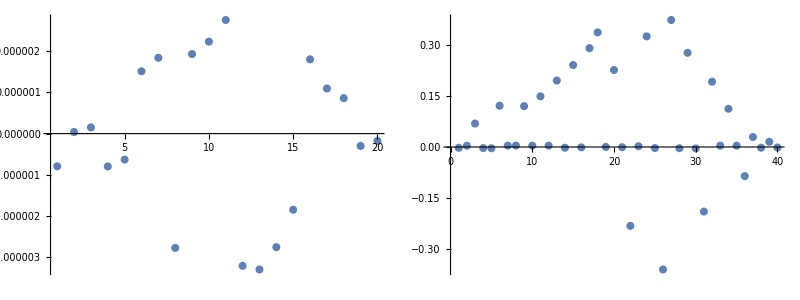

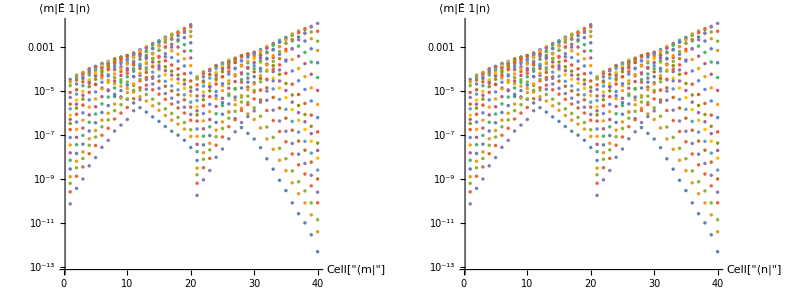

```mathematica
thresholdLIT=10^(-42);
{OμRHS,OrRHS,μsRHS}=normreg[thresholdLIT,DNorm];
{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];

{OμLHS,OrLHS,μsLHS}=normreg[thresholdLIT,LitNorm];
{λsLit,trfLit}=Eigensystem[(Transpose[OμLHS].LitHam).OμLHS];

inhomo=(2/mom) (Transpose[OμLHS].(CouplingBlock.OμRHS)).trfD[[1]];
Grid[{{ListPlot[inhomo,PlotRange->Full,ImageSize->ImgSize/2],ListPlot[trfD[[1]],ImageSize->ImgSize/2]}}]
Grid[{{ListLogPlot[Abs[CouplingBlock[[All,1;;]]],AxesLabel->{"Cell["⟨m|",ExpressionUUID->"d78adad6-8fa6-487d-b6f9-ae92439fff9a"]","⟨m|Ê 1|n⟩"},ImageSize->ImgSize/2,PlotRange->Full,GridLines->{{},{1}}],ListLogPlot[Abs[CouplingBlock[[1;;,All]]],AxesLabel->{"Cell["⟨n|",ExpressionUUID->"76e221ce-fdec-49de-953e-acd226ab6047"]","⟨m|Ê 1|n⟩"},ImageSize->ImgSize/2,PlotRange->Full,GridLines->{{},{1}}]}}]
```